# Lab 4: Differentiation -- Carter Colton

```mathematica
Clear["`*" ]
```

## Assignment 1: Fibonacci Numbers

You are probably familiar with the Fibonacci numbers: 1, 1, 2, 3, 5, 8, 13, 21, ..., where each number in the sequence is the sum of the two previous numbers. In Mathematica you can access the numbers via the Fibonacci command. You may or may not know that the ratio of succesive numbers (such as 8/5, 13/8, and 21/13) approaches a constant as the sequence progresses, but you can see that from this next graph. (I’ve added the Floor function into the plot command so that Fibonacci won’t calculate fractional Fibonacci numbers for the graph... which Mathematica can do but which aren’t relevant to the discussion. You won’t need the Floor function in order to find the limit.) Find the exact value of this constant, then google the number to learn its name.

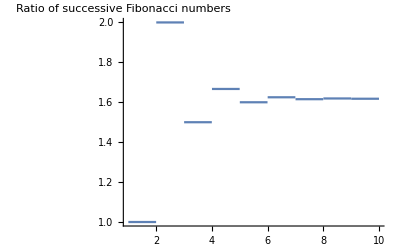

```mathematica
Plot[Fibonacci[Floor[n+1]]/Fibonacci[Floor[n]],{n,1,10},PlotRange->All,AxesOrigin->{0,0},AxesLabel->"Ratio of successive \n Fibonacci numbers"] (* the \n produces a line break *)
```

```mathematica
Limit[Fibonacci[(n+1)]/Fibonacci[n],n->Infinity]
```

1/2 (1+√5)

The value of this constant is the Golden Ratio

## Assignment 2: Taylor Series

Three of the most commonly used Taylor series in physics are sin(x), cos(x),  and e^x.  Let’s now use these series to prove Euler’s identity: e^ix=cos(x) + i sin(x). Specifically, use Mathematica to plug ix in place of x, in your Taylor’s series for e^x (say, to 20 terms). Then take the Taylor series of sin, multiply by i, and add it to the Taylor series of cosine. Show that when you do that, the two resulting series are the same.

```mathematica
Normal[Series[Exp[x],{x,0,20}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+x^12/479001600+x^13/6227020800+x^14/87178291200+x^15/1307674368000+x^16/20922789888000+x^17/355687428096000+x^18/6402373705728000+x^19/121645100408832000+x^20/2432902008176640000

```mathematica
Normal[Series[Exp[x]/.x->(I*x),{x,0,20}]]
```

1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120-x^6/720-(ⅈ x^7)/5040+x^8/40320+(ⅈ x^9)/362880-x^10/3628800-(ⅈ x^11)/39916800+x^12/479001600+(ⅈ x^13)/6227020800-x^14/87178291200-(ⅈ x^15)/1307674368000+x^16/20922789888000+(ⅈ x^17)/355687428096000-x^18/6402373705728000-(ⅈ x^19)/121645100408832000+x^20/2432902008176640000

```mathematica
(Normal[Series[Sin[x],{x,0,20}]]*I)+Normal[Series[Cos[x],{x,0,20}]]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000-x^18/6402373705728000+x^20/2432902008176640000+ⅈ (x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000)

## Assignment 3: Relativistic Kinetic Energy

In Physics 123 and/or 222, you learned that the true kinetic energy formula is  KE=E_tot-E_rest, where E_tot=γmc^2 and E_rest=mc^2.  In case you’ve forgotten, γ is the Lorentz factor, γ=1/sqrt(1-β^2) , and β is the velocity expressed as a fraction of the speed of light, β=v/c.  Use the Series command to calculate the kinetic energy for β<<1.  Show that when you replace beta with v/c, the first nonzero term in the expansion gives the familiar KE=1/2 mv^2 formula; if β is really small, that is all that’s important. What’s the second term in the expansion?

```mathematica
B=v/c
```

v/c

```mathematica
gamma=1/(Sqrt[1-(B^2)])
```

1/(√(1-v^2/c^2))

```mathematica
kineticenergy[v_]=gamma*mass*c^2-mass*c^2
```

-c^2 mass+(c^2 mass)/(√(1-v^2/c^2))

The first nonzero term here of the classic kinetic energy formula

```mathematica
Normal[Series[kineticenergy[v],v->0]]
```

(mass v^2)/2

The second term of the formula can be seen here

```mathematica
Normal[Series[kineticenergy[v],{v,0,5}]]
```

(mass v^2)/2+(3 mass v^4)/(8 c^2)

## Assignment 4: Calculating Derivatives

Do the following exercises, using a single D command in each case:
(a) Find the numerical value of the second derivative of f(x) = √(1+x^2), evaluated at x = 4.

(b) Plot J_0(x) along with its first derivative, from 0 to 20. Plot the J_0 function in blue and the derivative in red. Note that J_0(x) is a special function called a “zeroth-order Bessel function of the first kind” (see BesselJ). The subscript 0 indicates the order; the J indicates that it’s a Bessel function of the “first kind”. These kind of Bessel functions often arise in wave situations in optics and acoustics where there is cylindrical symmetry, for example the vibrations of a drum head. The derivatives of Bessel functions are other Bessel functions just like the derivatives of sines and cosines are other sines and cosines. 

Hint: a quick way to plot a function and its derivative is to use this syntax: 
f = function_of_x
df = D[f,x]
Plot[{f,df}, various_plot_options]

Here you don’t have to use pure argumentative functions (f[x_]=...), because simple algebraic expressions will work with the Plot command.

Something that won’t work when trying to plot a derivative, however, is sticking the derivative command inside the Plot command, like this command shown with sin(x) as the function for demonstration purposes: 
Plot[D[Sin[x],x]}, {x,0,10}]

If you try that command, you’ll get error messages such as “0.0002042857142857143` is not a valid variable.”  That’s because it’s choosing x=0.0002042857142857143 as a point for plotting the function before it tries to calculate the derivative of sin(x) with respect to x. So it’s attempting to calculate D[Sin[0.0002042857142857143],0.0002042857142857143], which clearly makes no sense.  However, you can use Evaluate to force Mathematica to first evaluate the derivative before plotting.  So, something like this command would work:
Plot[Evaluate[D[Sin[x],x]], {x,0,10}]

(c) Plot √(1+x^2) along with d^3/dx^3 √(1+x^2) , from -4 to 4. Plot the function in blue and the derivative in red. 
(d) Plot3D cos(x+y) along with ∂/(∂y)(∂/(∂x)cos(x+y)), from -π to π on both the x- and the y-axes. Plot the function in blue and the derivative in red. Note that if you're unfamiliar with partial derivatives, the curvy d in the d/dx sign means "take the derivative with respect to x, while treating y as a constant". Same sort of thing for the curvy d/dy.  Shortcut notation for that is ∂^2/(∂x∂y)cos(x+y) or ∂^2/(∂y∂x)cos(x+y)  (the order that you take the x and y derivatives generally does not matter).

```mathematica
derivative[x_]=√(1+x^2)
```

√(1+x^2)

```mathematica
N[D[derivative[x],{x,2}]/.x->4]
```

0.0142668

BesselJ[0,x]

-BesselJ[1,x]

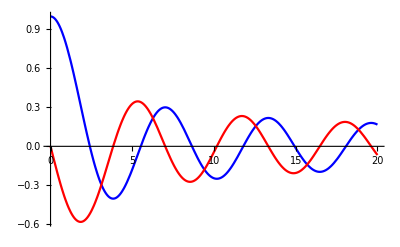

```mathematica
c[x_]=BesselJ[0,x]
df = D[c[x],x]
Plot[{c[x],df}, {x,0,20},PlotStyle->{Blue,Red}]
```

```mathematica
df3=D[derivative[x],{x,3}]
```

(3 x^3)/((1+x^2)^(5/2))-(3 x)/((1+x^2)^(3/2))

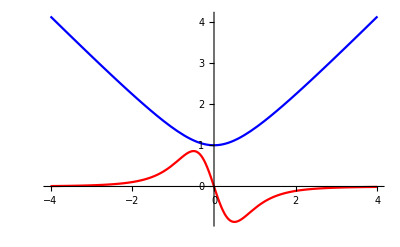

```mathematica
Plot[{derivative[x],df3}, {x,-4,4},PlotStyle->{Blue,Red}]
```

```mathematica
trig=Cos[x+y]
```

Cos[x+y]

```mathematica
dftrig=D[trig,x,y]
```

-Cos[x+y]

```mathematica
Plot3D[{trig,dftrig},{x,-Pi,Pi},{y,-Pi,Pi},PlotStyle->{Blue,Red}]
```

-Graphics3D-

## Assignment 5: Calculating the Field from the Potential: Electric Dipole

Consider the same electric dipole we looked at in the Plotting lab. For simplicity, again set 1/(4 πϵ_0) equal to 1. And we’ll again set z = 0 to just focus on the x-y plane.
(a) Define a function (or expression) that gives you the electric potential for two charges of opposite signs, a positive charge q = +1 at x = 0.5 and a negative charge q = -1 at x = -0.5. Remember to shift the potential from each charge away from the origin using the guidance from the introductory paragraph above (x replaced by x-x0, etc.).
(b) Define the components of the electric field as the negative derivatives of the potential. Verify that StreamPlot gives you the same plot of the field lines it did in the last lab. Review the Plotting lab and/or consult the help file for the StreamPlot command to remind yourself what the input arguments need to be.
(c) Make a ContourPlot of the electric potential in the xy plane with ContourShading→None, and plot it on the same graph as the StreamPlot (the Show command will be helpful). You should be able to verify that the electric field lines are always perpendicular to the equipotential contours, as taught in Physics 220.

```mathematica
eandm =(x-.5)/((x-.5)^2+y^2)^1.5-(x+.5)/((x+.5)^2+y^2)^1.5
```

(-0.5+x)/(((-0.5+x)^2+y^2)^1.5)-(0.5+x)/(((0.5+x)^2+y^2)^1.5)

```mathematica
dfeandmx=-D[eandm, x]
```

(3. (-0.5+x)^2)/(((-0.5+x)^2+y^2)^2.5)-1/(((-0.5+x)^2+y^2)^1.5)-(3. (0.5+x)^2)/(((0.5+x)^2+y^2)^2.5)+1/(((0.5+x)^2+y^2)^1.5)

```mathematica
dfeandmy=-D[eandm, y]
```

(3. (-0.5+x) y)/(((-0.5+x)^2+y^2)^2.5)-(3. (0.5+x) y)/(((0.5+x)^2+y^2)^2.5)

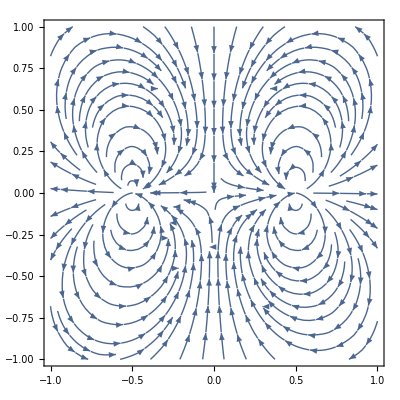

```mathematica
StreamPlot[{dfeandmx,dfeandmy},{x,-1,1},{y,-1,1}]
```

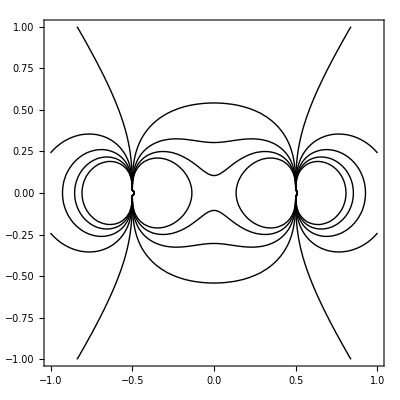

```mathematica
ContourPlot[{eandm},{x,-1,1},{y,-1,1},ContourShading->None]
```

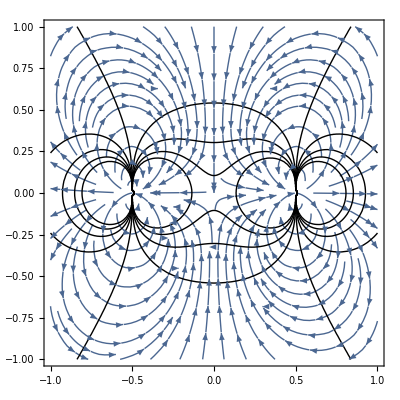

```mathematica
Show[StreamPlot[{dfeandmx,dfeandmy},{x,-1,1},{y,-1,1}],ContourPlot[{eandm},{x,-1,1},{y,-1,1},ContourShading->None]]
```

## Assignment 6: Ten Random Charges

Now that you know what you're doing, you should be able to fairly easily modify your code to use the potential function given below. It will give you the potential due to 10 random charges (positive and negative) at random positions. Plot the equipotential contours along with the field lines. Make two plots: one so you can see things close to the charges (say, x and y both go from -1 to 1), and one so you can see things far from the charges (say, x and y both go from -10 to 10). Why do the potential and field lines behave the way they do on the “zoomed out” graph?

```mathematica
Vbase = q/Sqrt[x^2+y^2];
V = Sum[Vbase /. {q-> RandomReal[{-1,1}],x-> x-RandomReal[{-1,1}], y-> y-RandomReal[{-1,1}]}, {n,1,10}];
```

```mathematica
Vx=-D[V,x]
```

(0.511352 (0.425543+x))/(((0.425543+x)^2+(-0.931467+y)^2)^(3/2))+(0.000248163 (-0.434194+x))/(((-0.434194+x)^2+(-0.709037+y)^2)^(3/2))-(0.701586 (-0.462909+x))/(((-0.462909+x)^2+(-0.62008+y)^2)^(3/2))-(0.146127 (0.781401+x))/(((0.781401+x)^2+(-0.457676+y)^2)^(3/2))+(0.604311 (-0.15369+x))/(((-0.15369+x)^2+(-0.314822+y)^2)^(3/2))-(0.0312213 (-0.625955+x))/(((-0.625955+x)^2+(-0.192052+y)^2)^(3/2))+(0.88005 (0.59699+x))/(((0.59699+x)^2+(-0.109224+y)^2)^(3/2))+(0.812687 (0.57978+x))/(((0.57978+x)^2+(-0.0712282+y)^2)^(3/2))-(0.616482 (0.263222+x))/(((0.263222+x)^2+(0.391259+y)^2)^(3/2))+(0.315298 (0.510604+x))/(((0.510604+x)^2+(0.522622+y)^2)^(3/2))

```mathematica
Vy=-D[V,y]
```

(0.511352 (-0.931467+y))/(((0.425543+x)^2+(-0.931467+y)^2)^(3/2))+(0.000248163 (-0.709037+y))/(((-0.434194+x)^2+(-0.709037+y)^2)^(3/2))-(0.701586 (-0.62008+y))/(((-0.462909+x)^2+(-0.62008+y)^2)^(3/2))-(0.146127 (-0.457676+y))/(((0.781401+x)^2+(-0.457676+y)^2)^(3/2))+(0.604311 (-0.314822+y))/(((-0.15369+x)^2+(-0.314822+y)^2)^(3/2))-(0.0312213 (-0.192052+y))/(((-0.625955+x)^2+(-0.192052+y)^2)^(3/2))+(0.88005 (-0.109224+y))/(((0.59699+x)^2+(-0.109224+y)^2)^(3/2))+(0.812687 (-0.0712282+y))/(((0.57978+x)^2+(-0.0712282+y)^2)^(3/2))-(0.616482 (0.391259+y))/(((0.263222+x)^2+(0.391259+y)^2)^(3/2))+(0.315298 (0.522622+y))/(((0.510604+x)^2+(0.522622+y)^2)^(3/2))

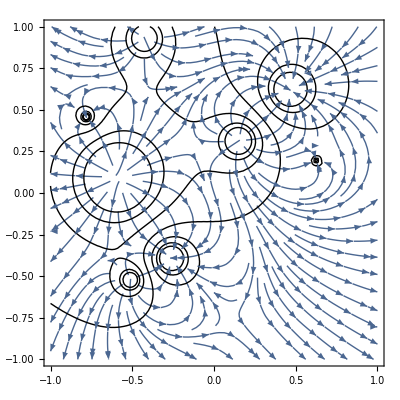

```mathematica
Show[StreamPlot[{Vx,Vy},{x,-1,1},{y,-1,1}],ContourPlot[{V},{x,-1,1},{y,-1,1},ContourShading->None,ColorFunction->"Rainbow"]]
```

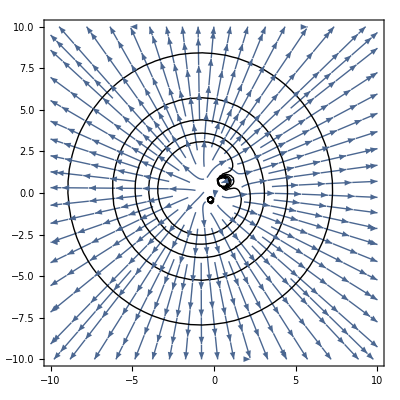

```mathematica
Show[StreamPlot[{Vx,Vy},{x,-10,10},{y,-10,10}],ContourPlot[{V},{x,-10,10},{y,-10,10},ContourShading->None,ColorFunction->"Rainbow"]]
```

The electric potential and field lines obey the way they do here because electric potential lines are always perpendicular to electric field lines.

## Assignment 7: Projectile with Air Resistance

(a) Test to make sure that y(t) function makes sense by evaluating it in the limit as b→ 0. It should match the Phys 121 equation. 
(b) Make plots of y(t), v(t), and a(t) for a 1 kg object, starting at y0 = 0 and with initial velocity v0 = 100 m/s. (Remember a_y=-g, so g =+9.8 m/s^2.)  Let t range from 0 to 20 s. Make one set of plots for b = 0.00001 kg/s, and another set for b = 0.3 kg/s. 
(c) For the condition where b = 0.3, find the time it takes the object to reach the maximum height, the time it takes to return to the ground, and the velocity it has when it reaches the ground (note how kinetic energy is not conserved!).

Hint: Here's a slick way to generate three plots at once, assuming f1(t), f2(t), and f3(t) are previously-defined pure functions:  Plot[# ,{t,0,20}] & /@{f1[t], f2[t], f3[t]}.   Or if f1, f2, and f3 are expressions, you can do it this way: Plot[# ,{t,0,20}] & /@{f1, f2, f3}.  It creates a three element array, each element of which is a plot. Remember the /@ notation refers to the Map function, and is extremely helpful in getting another function (e.g. Plot) to be evaluated for each of the elements in a list.

```mathematica
Clear["`*"]   (* just in case you've defined y as something that it won't like *)
DSolve[  {-m g -b y'[t] == m y''[t] , y[0]==y0, y'[0]==v0}  , y[t], t]
y[t_] = y [t]/. %[[1]]  //Expand   (* this is needed to define y as a function of t because the output of DSolve is in a weird format *)
```

{{y[t]→(ⅇ^(-(b t)/m) (-g m^2+ⅇ^((b t)/m) g m^2-b ⅇ^((b t)/m) g m t-b m v0+b ⅇ^((b t)/m) m v0+b^2 ⅇ^((b t)/m) y0))/b^2}}

(g m^2)/b^2-(ⅇ^(-(b t)/m) g m^2)/b^2-(g m t)/b+(m v0)/b-(ⅇ^(-(b t)/m) m v0)/b+y0

This matches the physics 121 equation

```mathematica
Limit[y[t],b->0]
```

-(g t^2)/2+t v0+y0

```mathematica
y0=0
m=1
v0=100
g=9.8
```

0

1

100

9.8

```mathematica
v[t_]=D[y[t],t]
```

-9.8/b+100 ⅇ^(-b t)+(9.8 ⅇ^(-b t))/b

```mathematica
a[t_]=D[v[t],t]
```

-9.8 ⅇ^(-b t)-100 b ⅇ^(-b t)

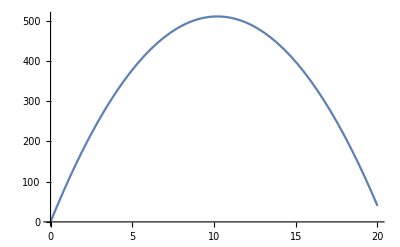
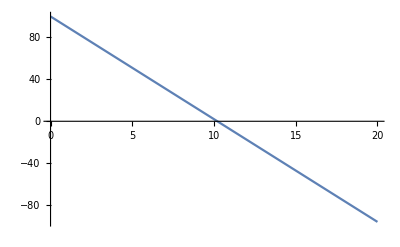
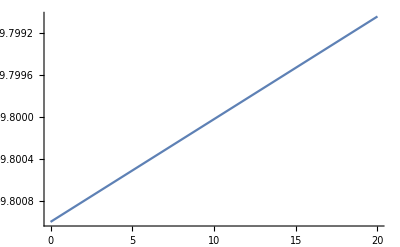

```mathematica
Plot[# ,{t,0,20}] & /@{y[t]/.b->0.00001, v[t]/.b->0.00001, a[t]/.b->0.00001}
```

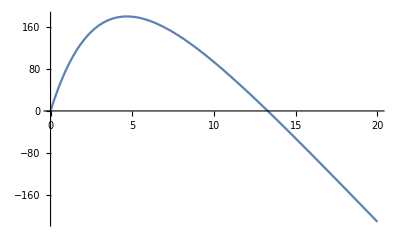
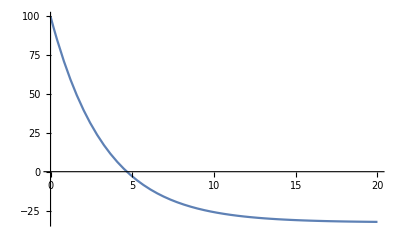
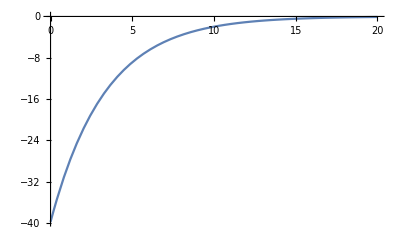

```mathematica
Plot[# ,{t,0,20}] & /@{y[t]/.b->0.3, v[t]/.b->0.3, a[t]/.b->0.3}
```

This is the time it takes the object to reach maximum height

```mathematica
FindRoot[v[t]/.b->0.3,{t,5}]
```

{t→4.67162}

This is the time it takes the object to return to the ground

```mathematica
FindRoot[y[t]/.b->0.3,{t,13}]
```

{t→13.2859}

This is the velocity it has when it reaches the ground

```mathematica
N[v[t]/.{b->0.3,t->13.2859}]
```

-30.202

## Assignment 8: Using the Maxwell-Boltzmann Velocity Distribution

(a) To get a better feel for the Maxwell-Boltzmann distribution, make a plot of it for nitrogen molecules at temperatures of 77K (the condensing point), 300K (room temperature), and 3000K (roughly the temperature of the filament inside an incandescent light bulb). Hint: the molecular mass of nitrogen molecules is 28.01 AMU; you’ll need to convert that to kg.
(b) The phrase “most probable speed” refers to where the f(v) distribution is peaked. Without using any numbers at all now, take the derivative of f(v), set it equal to zero, and solve for v. You should obtain the v_mp formula given above.

f(v)=sqrt(2/π(m/kT)^3)v^2 exp(-mv^2/(2kT))

```mathematica
m=28.01*(1.6605*10^-27)
```

4.65106×10^-26

```mathematica
k=1.380649×10^-23
```

1.38065×10^-23

```mathematica
f[v_]=Sqrt[(2/Pi)*(m/(k*T))^3]*v^2*Exp[-(m*v^2)/(2*k*T)]
```

0.000156007 ⅇ^(-(0.00168437 v^2)/T) √(1/T^3) v^2

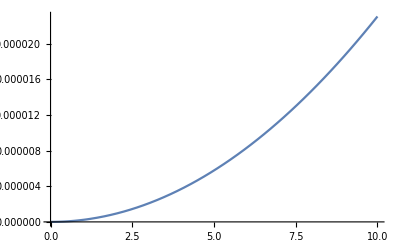
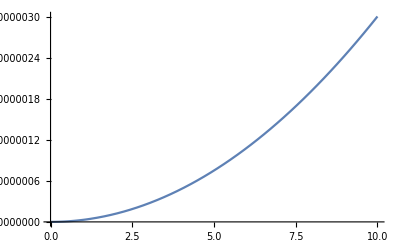
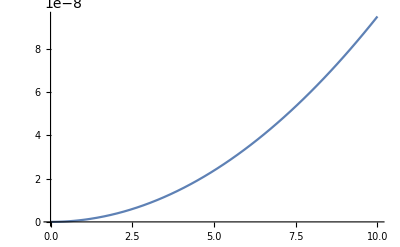

```mathematica
Plot[# ,{v,0,10}] & /@{f[v]/.T->77, f[v]/.T->300, f[v]/.T->3000}
```

```mathematica
Clear["`*"]
```

```mathematica
f[v_]=Sqrt[(2/Pi)*(m/(k*T))^3]*v^2*Exp[-(m*v^2)/(2*k*T)]
```

ⅇ^(-(m v^2)/(2 k T)) √(2/π) √(m^3/(k^3 T^3)) v^2

```mathematica
D[f[v],v]
```

2 ⅇ^(-(m v^2)/(2 k T)) √(2/π) √(m^3/(k^3 T^3)) v-(ⅇ^(-(m v^2)/(2 k T)) m √(2/π) √(m^3/(k^3 T^3)) v^3)/(k T)

```mathematica
Solve[%==0,v]
```

{{v→0},{v→-(√2 √k √T)/(√m)},{v→(√2 √k √T)/(√m)}}

The last root of the equation is the v_mp formula: v_mp=sqrt((2kT)/m)